```mathematica
f[n_,k_]=1+√(1-1/k) (-1+(8 n)/3)+(1-16/9 (-1+k) n (-1+4 n))/(2 √(1-1/k) k (1+(8 n)/3))
```

1+√(1-1/k) (-1+(8 n)/3)+(1-16/9 (-1+k) n (-1+4 n))/(2 √(1-1/k) k (1+(8 n)/3))

```mathematica
f[k_]=√k(1+((8n)/3-1)√(1-1/k)+(1-16/9 n(k-1)(4n-1))/(2k √(1-1/k)((8n)/3+1)))/.n->IntegerPart[1/8(1+√(1+9/(k-1)))]
```

√k (1+√(1-1/k) (-1+8/3 IntegerPart[1/8 (1+√(1+9/(-1+k)))])+(1-16/9 (-1+k) IntegerPart[1/8 (1+√(1+9/(-1+k)))] (-1+4 IntegerPart[1/8 (1+√(1+9/(-1+k)))]))/(2 √(1-1/k) k (1+8/3 IntegerPart[1/8 (1+√(1+9/(-1+k)))])))

```mathematica
f[0,1]
```

Power::infy: Infinite expression 1/√0 encountered.

ComplexInfinity

```mathematica
f[1,k]//FullSimplify
```

(7+30 √(-1+k) √k+2 k)/(30 √(-1+k) √k)

```mathematica
{%8,%10}/.k->19/16//N
```

{1.66227,-0.456986}

```mathematica
δl/(u0+2n u2)/.u2->(4u0)/3/.δl->l-(8 u0^2)/(9g)(4 n^2-n)/.u0->v0 √(1-1/k)
```

(l-(8 (1-1/k) (-n+4 n^2) v0^2)/(9 g))/(√(1-1/k) v0+8/3 √(1-1/k) n v0)

```mathematica
Plot[f[x],{x,1,1.5},Axes->False,Frame->True,PlotRange->{{1,1.5},{1,2}},ImageSize->{720,480},FrameTicks->{{Automatic,None},{Automatic,None}},FrameLabel->{Style["v_0^2/2gl",24],Style["gt/v_0",24]},FrameTicksStyle->20,PlotStyle->Thickness[0.005]]
```

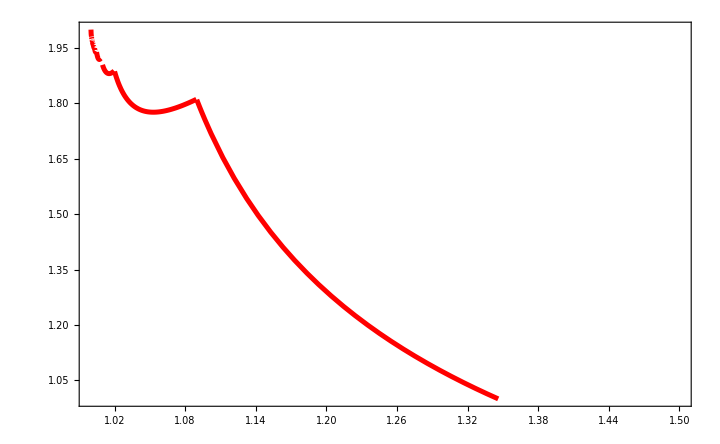

```mathematica
Plot[{f[x^2]},{x,1,1.5},Axes->False,Frame->True,PlotRange->{{1,1.5},{1,2}},ImageSize->{720,480},FrameTicks->{{Automatic,None},{Automatic,None}},FrameTicksStyle->28,PlotStyle->{Red,Thickness[0.005]}]
```

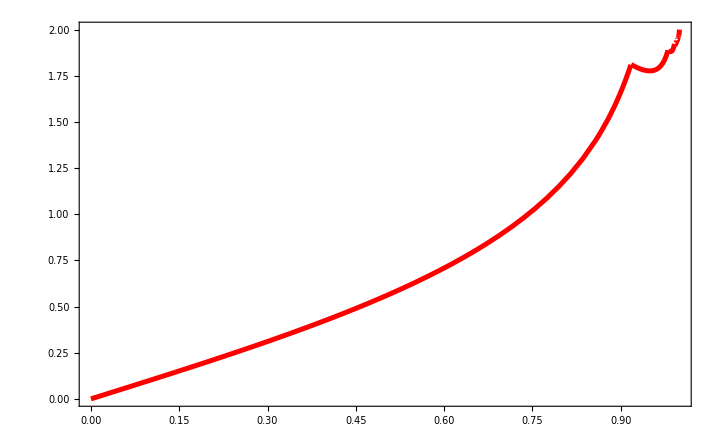

```mathematica
Plot[{f[1/x^2]},{x,0,1},Axes->False,Frame->True,PlotRange->{{0,1},{0,2}},ImageSize->{720,480},FrameTicks->{{Automatic,None},{Automatic,None}},FrameTicksStyle->28,PlotStyle->{Red,Thickness[0.005]}]
```

```mathematica
IntegerPart[1/8(1+√(1+9/(k-1)))]/.k->1
```

Power::infy: Infinite expression 1/0 encountered.

ComplexInfinity

```mathematica
f[x]
```

1+√(1-1/x) (-1+8/3 IntegerPart[1/8 (1+√(1+9/(-1+x)))])+(1-16/9 (-1+x) IntegerPart[1/8 (1+√(1+9/(-1+x)))] (-1+4 IntegerPart[1/8 (1+√(1+9/(-1+x)))]))/(2 √(1-1/x) x (1+8/3 IntegerPart[1/8 (1+√(1+9/(-1+x)))]))

```mathematica
t1=(v0-u0)/g/.u0->v0 √(1-1/k)
```

(v0-√(1-1/k) v0)/g

```mathematica
t2=(1-16/9 n(k-1)(4n-1))/(2k √(1-1/k)((8n)/3+1))/.n->IntegerPart[1/8(1+√(1+9/(k-1)))]
```

(1-16/9 (-1+k) IntegerPart[1/8 (1+√(1+9/(-1+k)))] (-1+4 IntegerPart[1/8 (1+√(1+9/(-1+k)))]))/(2 √(1-1/k) k (1+8/3 IntegerPart[1/8 (1+√(1+9/(-1+k)))]))

```mathematica
t=t2+1+(8n/3-1)√(1-1/k)/.n->IntegerPart[1/8(1+√(1+9/(k-1)))]
```

1+√(1-1/k) (-1+8/3 IntegerPart[1/8 (1+√(1+9/(-1+k)))])+(1-16/9 (-1+k) IntegerPart[1/8 (1+√(1+9/(-1+k)))] (-1+4 IntegerPart[1/8 (1+√(1+9/(-1+k)))]))/(2 √(1-1/k) k (1+8/3 IntegerPart[1/8 (1+√(1+9/(-1+k)))]))

```mathematica
f[0,19/16]//N
```

1.66227

```mathematica
g1[x_]=f[1,x]
```

1+5/3 √(1-1/x)+(3 (1-16/3 (-1+x)))/(22 √(1-1/x) x)

```mathematica
g1[19/16]//N
```

1.66227

```mathematica
g1'[19/16]//N
```

-0.0540798

```mathematica
g0'[19/16]//N
```

-4.16414

```mathematica
f1[p_]=1+((8n)/3-1)p+(1-p^2(1+16/9 n(4n-1)))/(2p((8n)/3+1))/.n->IntegerPart[1/8(1+√(1+(9(1-p^2))/p^2))]
```

1+p (-1+8/3 IntegerPart[1/8 (1+√(1+(9 (1-p^2))/p^2))])+(1-p^2 (1+16/9 IntegerPart[1/8 (1+√(1+(9 (1-p^2))/p^2))] (-1+4 IntegerPart[1/8 (1+√(1+(9 (1-p^2))/p^2))])))/(2 p (1+8/3 IntegerPart[1/8 (1+√(1+(9 (1-p^2))/p^2))]))

```mathematica
Plot[f1[x],{x,0,0.01},ImageSize->{3000,2000}]
```

```mathematica
g[k_]=√k(1+((4n)/3-1)√(1-1/k)+(1-16/9 n(n-1)(k-1))/(2k*(4n)/3 √(1-1/k)))/.n->IntegerPart[1/2(1+√(1+9/(4(k-1))))]
```

√k (1+√(1-1/k) (-1+4/3 IntegerPart[1/2 (1+√(1+9/(4 (-1+k))))])+(3 (1-16/9 (-1+k) (-1+IntegerPart[1/2 (1+√(1+9/(4 (-1+k))))]) IntegerPart[1/2 (1+√(1+9/(4 (-1+k))))]))/(8 √(1-1/k) k IntegerPart[1/2 (1+√(1+9/(4 (-1+k))))]))

```mathematica
Plot[f[x],{x,1,100000
}]
```

-Graphics-

```mathematica
Limit[g[x],x->∞]
```

4/3

```mathematica
Series[g[x],{x,1,1}]
```

1/IntegerPart[1/2 (1+√(1+9/(4 (-1+x))))](IntegerPart[1/2 (1+√(1+9/(4 (-1+x))))]^2 (-(2 √(x-1))/3+O[x-1]^(3/2))+IntegerPart[1/2 (1+√(1+9/(4 (-1+x))))]^2 ((4 √(x-1))/3+O[x-1]^(3/2))+IntegerPart[1/2 (1+√(1+9/(4 (-1+x))))] (1+(5 √(x-1))/3+O[x-1]^(3/2))+(3/(8 √(x-1))-(3 √(x-1))/16+O[x-1]^(3/2)))

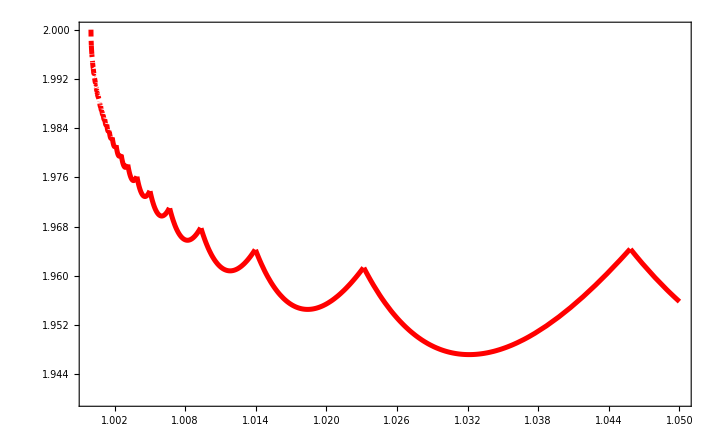

```mathematica
Plot[{g[x^2]},{x,1,1.05},Axes->False,Frame->True,PlotRange->{{1,1.05},{1.94,2}},ImageSize->{720,480},FrameTicks->{{Automatic,None},{Automatic,None}},FrameTicksStyle->28,PlotStyle->{Red,Thickness[0.005]}]
```

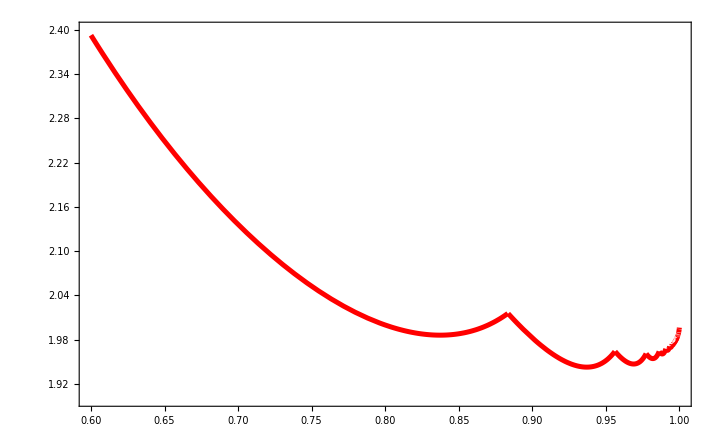

```mathematica
Plot[{g[1/x^2]},{x,0.6,1},Axes->False,Frame->True,PlotRange->{{0.6,1},{1.9,2.4}},ImageSize->{720,480},FrameTicks->{{Automatic,None},{Automatic,None}},FrameTicksStyle->28,PlotStyle->{Red,Thickness[0.005]}]
```

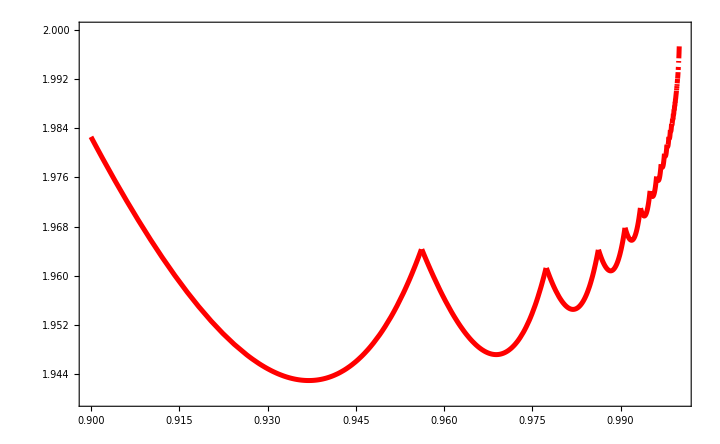

```mathematica
Plot[{g[1/x^2]},{x,0.9,1},Axes->False,Frame->True,PlotRange->{{0.9,1},{1.94,2}},ImageSize->{720,480},FrameTicks->{{Automatic,None},{Automatic,None}},FrameTicksStyle->28,PlotStyle->{Red,Thickness[0.005]}]
```

```mathematica
g[41/9]//N
```

2.96179

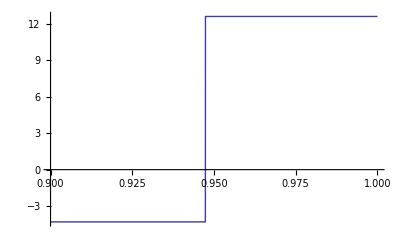

```mathematica
Plot[IntegerPart'[x],{x,0.9,1}]
```